[Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x-y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x+y/2]ⅆy];
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]-p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (-x Cos[θ]+p Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after heterodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]+s Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]);
```

```mathematica
xmat=Module[{M},
M=]
```

```mathematica
(* Gaussian integrals *)
int[v_,w_]:=integral@@ (v~Join~w);
(*∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-(A11 x^2+ A21 p^2+B11 x +B21 p +B121 x p +C1))ⅇ^(-(A12 x^2+ A22 p^2+B12 x +B22 p +B122 x p +C2))ⅆxⅆp*)
integral[A11_, A21_ ,B11_ ,B21_ ,B121_ , C1_,A12_, A22_ ,B12_ ,B22_ ,B122_ , C2_]:=(2 ⅇ^((B11^2+2 B11 B12+B12^2+(B11 (B121+B122)+B12 (B121+B122)-2 (A11+A12) (B21+B22))^2/(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)-4 A11 C1-4 A12 C1-4 A11 C2-4 A12 C2)/(4 (A11+A12))) π)/(√(A11+A12) √(1/(A11+A12)(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)));(*ConditionalExpression[(2 ⅇ^((B11^2+2 B11 B12+B12^2+(B11 (B121+B122)+B12 (B121+B122)-2 (A11+A12) (B21+B22))^2/(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)-4 A11 C1-4 A12 C1-4 A11 C2-4 A12 C2)/(4 (A11+A12))) π)/(√(A11+A12) √((4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)/(A11+A12))), Re[(-4 A11 (A21+A22)-4 A12 (A21+A22)+(B121+B122)^2)/(A11+A12)]≤0];*)
```

```mathematica
∫_(-Δp/2)^(Δp/2) ⅇ^(-(A1 x^2+ A2 p^2+B1 x +B2 p +B12 x p +C))ⅆp
```

(ⅇ^((B2^2+2 B12 B2 x+B12^2 x^2-4 A2 (C+x (B1+A1 x)))/(4 A2)) √π (-Erf[(B2+B12 x-A2 Δp)/(2 √A2)]+Erf[(B2+B12 x+A2 Δp)/(2 √A2)]))/(2 √A2)

```mathematica
Collect[(B2^2+2 B12 B2 x+B12^2 x^2-4 A2 (C+x (B1+A1 x)))/(4 A2),x]
Collect[(B2+B12 x-A2 Δp)/(2 √A2),x]
Collect[(B2+B12 x+A2 Δp)/(2 √A2),x]
```

(B2^2-4 A2 C)/(4 A2)+((-4 A2 B1+2 B12 B2) x)/(4 A2)+((-4 A1 A2+B12^2) x^2)/(4 A2)

(B12 x)/(2 √A2)+(B2-A2 Δp)/(2 √A2)

(B12 x)/(2 √A2)+(B2+A2 Δp)/(2 √A2)

```mathematica
∫_(-Δx/2)^(Δx/2) ⅇ^(a x^2+b x+c)(Erf[d x+e]-Erf[d x+f])ⅆx
```

∫_(-Δx/2)^(Δx/2) ⅇ^(c+b x+a x^2) (Erf[e+d x]-Erf[f+d x])ⅆx

```mathematica
∫_(-Δx/2)^(Δx/2) %ⅆx
```

$Aborted

#### [Calc] Checking normalization

```mathematica
(* ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(π ϵ)ⅇ^(-1/ϵ(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x2,p2,s]ⅆp2ⅆx2 *)(*1/(π^3 ϵ)∫_(-∞)^∞ ⅇ^(-(p^2-2 p p2+x^2-2 x x2+x2^2+p1^2 ϵ+x1^2 ϵ+x2^2 ϵ+p2^2 (1+ϵ))/ϵ)(ⅇ^(-2 α^2)(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))+s(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2 *)
```

```mathematica
ClearAll[v,expr];
expr=ⅇ^(-(p^2-2 p p2+x^2-2 x x2+x2^2+p1^2 ϵ+x1^2 ϵ+x2^2 ϵ+p2^2 (1+ϵ))/ϵ);
Module[{M},
M=CoefficientList[Collect[-Exponent[expr,ⅇ],{x2,p2}],{x2,p2},{3,3}];
v={M[[3,1]],M[[1,3]],M[[2,1]],M[[1,2]],M[[2,2]],M[[1,1]]}
];
```

```mathematica
ClearAll[w,expr];
W=1/(π^3 ϵ){ⅇ^(-2 α^2),ⅇ^(-2 α^2),s,s};
expr[1]=ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]));
expr[2]=ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]));
expr[3]=ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]));
expr[4]=ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]));
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x2,p2}],{x2,p2},{3,3}]&/@Range[4];
(w[#]={M[[#,3,1]],M[[#,1,3]],M[[#,2,1]],M[[#,1,2]],M[[#,2,2]],M[[#,1,1]]})&/@Range[4]
];
```

```mathematica
Simplify[∑_(i=1)^4 W[[i]]int[v,w[i]]]/.{x->x2,p->p2}
```

1/(π^2 (1+ϵ))ⅇ^(-2 α^2) (ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s)

```mathematica
(* Tracing over mode 2 *)
```

```mathematica
ClearAll[w,expr];
W=1/(π^2 (1+ϵ))ⅇ^(-2 α^2){1,1,s,s};
expr[1]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ));
expr[2]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ));
expr[3]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ));
expr[4]=ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ));
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x2,p2}],{x2,p2},{3,3}]&/@Range[4];
(w[#]={M[[#,3,1]],M[[#,1,3]],M[[#,2,1]],M[[#,1,2]],M[[#,2,2]],M[[#,1,1]]})&/@Range[4]
];
Expand[∑_(i=1)^4 W[[i]]int[{0,0,0,0,0,0},w[i]]]
```

(ⅇ^(-2 α^2+1/4 (1+ϵ) ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]-2 √2 p1 t α (1+ϵ) Sin[θ]))/(1+ϵ)^2)))/π+(ⅇ^(-2 α^2+1/4 (1+ϵ) ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+2 √2 p1 t α (1+ϵ) Sin[θ]))/(1+ϵ)^2)))/π+(ⅇ^(-2 α^2+1/4 (1+ϵ) (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 p1 t α (1+ϵ) Cos[θ]-2 ⅈ √2 t x1 α (1+ϵ) Sin[θ]))/(1+ϵ)^2)) s)/π+(ⅇ^(-2 α^2+1/4 (1+ϵ) (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 p1 t α (1+ϵ) Cos[θ]+2 ⅈ √2 t x1 α (1+ϵ) Sin[θ]))/(1+ϵ)^2)) s)/π

```mathematica
(* Tracing over mode 1 *)
```

```mathematica
W=1/π{1,1,s,s};
expr[1]=ⅇ^(-2 α^2+1/4 (1+ϵ) ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]-2 √2 p1 t α (1+ϵ) Sin[θ]))/(1+ϵ)^2));
expr[2]=ⅇ^(-2 α^2+1/4 (1+ϵ) ((8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2+(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+2 √2 p1 t α (1+ϵ) Sin[θ]))/(1+ϵ)^2));
expr[3]=ⅇ^(-2 α^2+1/4 (1+ϵ) (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 p1 t α (1+ϵ) Cos[θ]-2 ⅈ √2 t x1 α (1+ϵ) Sin[θ]))/(1+ϵ)^2));
expr[4]=ⅇ^(-2 α^2+1/4 (1+ϵ) (-(8 r^2 α^2 Cos[θ]^2)/(1+ϵ)^2-(8 r^2 α^2 Sin[θ]^2)/(1+ϵ)^2-(4 (p1^2+x1^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 p1 t α (1+ϵ) Cos[θ]+2 ⅈ √2 t x1 α (1+ϵ) Sin[θ]))/(1+ϵ)^2));
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x1,p1}],{x1,p1},{3,3}]&/@Range[4];
(w[#]={M[[#,3,1]],M[[#,1,3]],M[[#,2,1]],M[[#,1,2]],M[[#,2,2]],M[[#,1,1]]})&/@Range[4]
];
Simplify[∑_(i=1)^4 W[[i]]int[{0,0,0,0,0,0},w[i]],r^2==1-t^2]
```

2+2 ⅇ^(-2 α^2) s

```mathematica
(* ϵ Gaussian filetered 2 mode normlaized Wigner: Wn = ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(π ϵ)ⅇ^(-1/ϵ(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x,p,s]ⅆpⅆx *)
Wn[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=1/(2(1+s ⅇ^(-2 α^2)))1/(π^2 (1+ϵ))ⅇ^(-2 α^2) (ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s);
```

#### [Calc] Heralding on Δ range in x_2 around the origin

```mathematica
(* Leaving out the pre factor for now *)
```

```mathematica
ClearAll[t,r,α,Δ, θ,Wn,Wh]
∫_(-Δp/2)^(Δp/2) ((ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]-2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 α (p2 r-t x1 (1+ϵ)) Cos[θ]+2 √2 α (r x2+p1 t (1+ϵ)) Sin[θ])/(1+ϵ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2-2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+2 ⅈ √2 α (p2 r-t x1 (1+ϵ)) Sin[θ])/(1+ϵ)) s))ⅆp2
```

-1/2 ⅇ^(-(p1^2+x1^2+x2^2-r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]-r^2 α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(-Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]+1/2 ⅇ^(-(p1^2+x1^2+x2^2-r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]-r^2 α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]-1/2 ⅇ^(-(p1^2+x1^2+x2^2-r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]-r^2 α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+1/2 ⅇ^(-(p1^2+x1^2+x2^2-r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 r^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]-r^2 α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+s (-1/2 ⅇ^(-(p1^2+x1^2+x2^2-2 α^2+r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-r^2 α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(-Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+1/2 ⅇ^(-(p1^2+x1^2+x2^2-2 α^2+r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-r^2 α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))])+s (-1/2 ⅇ^(-(p1^2+x1^2+x2^2-2 α^2+r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-r^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+1/2 ⅇ^(-(p1^2+x1^2+x2^2-2 α^2+r^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 r^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]-r^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) √π √(1+ϵ) Erf[(Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))])

```mathematica
Simplify[%,r^2+t^2==1]
```

1/2 ⅇ^(-(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ)) √π √(1+ϵ) (ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+p1 t (1+ϵ)) Cos[θ]-√2 (2 r x2+t (2 p1+ⅈ x1) (1+ϵ)) Sin[θ]))/(1+ϵ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+t (p1-2 ⅈ x1) (1+ϵ)) Cos[θ]-ⅈ √2 t x1 (1+ϵ) Sin[θ]))/(1+ϵ)) (-Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^((2 α (α+α ϵ+√2 r x2 (2 ⅈ Cos[θ]+Sin[θ])+√2 t (1+ϵ) ((2 ⅈ p1+x1) Cos[θ]+(p1+2 ⅈ x1) Sin[θ])))/(1+ϵ)) s (-Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^((2 α (α+α ϵ+√2 r x2 Sin[θ]+√2 t (1+ϵ) (x1 Cos[θ]+p1 Sin[θ])))/(1+ϵ)) s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]))

```mathematica
Exp[Simplify[-1/(1+ϵ)(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+p1 t (1+ϵ)) Cos[θ]-√2 (2 r x2+t (2 p1+ⅈ x1) (1+ϵ)) Sin[θ]))/(1+ϵ)]]
Exp[Simplify[-1/(1+ϵ)(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))-(2 α ((-1+t^2) α (1+2 ϵ)-ⅈ √2 (r x2+t (p1-2 ⅈ x1) (1+ϵ)) Cos[θ]-ⅈ √2 t x1 (1+ϵ) Sin[θ]))/(1+ϵ)]]
```

ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ))

ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ))

```mathematica
Exp[Simplify[-1/(1+ϵ)(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))+(2 α (α+α ϵ+√2 r x2 (2 ⅈ Cos[θ]+Sin[θ])+√2 t (1+ϵ) ((2 ⅈ p1+x1) Cos[θ]+(p1+2 ⅈ x1) Sin[θ])))/(1+ϵ)]]
Exp[Simplify[-1/(1+ϵ)(p1^2+x1^2+x2^2+α^2+p1^2 ϵ+x1^2 ϵ+2 α^2 ϵ-α^2 Cos[2 θ]+t^2 α^2 (-1-2 ϵ+Cos[2 θ])+2 √2 r x2 α (ⅈ Cos[θ]+Sin[θ])+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))+(2 α (α+α ϵ+√2 r x2 Sin[θ]+√2 t (1+ϵ) (x1 Cos[θ]+p1 Sin[θ])))/(1+ϵ)]]
```

ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ))

ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ))

```mathematica
1/2  √π √(1+ϵ) (ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ))(-Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) s (-Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]))
```

```mathematica
(* Leaving out the pre-factor again *)
```

```mathematica
∫_(-Δx/2)^(Δx/2) (ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ))(-Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) s (-Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ)) s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]))ⅆx2
```

$Aborted

```mathematica
(*∫_(-Δ/2)^(Δ/2) ⅇ^(-(a x^2+b x +c))ⅆx*)
```

```mathematica
int1[v_,Δ_]:=(ⅇ^(v[[2]]^2/(4 v[[1]])-v[[3]]) √π (-Erf[(v[[2]]-v[[1]] Δ)/(2 √v[[1]])]+Erf[(v[[2]]+v[[1]] Δ)/(2 √v[[1]])]))/(2 √v[[1]]);
```

```mathematica
expr[1]=ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ+2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]-2 √2 r x2 α Sin[θ]-2 √2 p1 t α ϵ Sin[θ])/(1+ϵ));
expr[2]=ⅇ^(-(p1^2+x1^2+x2^2-α^2+t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 α^2 ϵ+2 t^2 α^2 ϵ-2 √2 t x1 α (1+ϵ) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 √2 p1 t α Sin[θ]+2 √2 r x2 α Sin[θ]+2 √2 p1 t α ϵ Sin[θ])/(1+ϵ));
expr[3]=ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ-2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]-2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ));
expr[4]=ⅇ^(-(p1^2+x1^2+x2^2-α^2-t^2 α^2+p1^2 ϵ+x1^2 ϵ-2 t^2 α^2 ϵ+2 ⅈ √2 α (r x2+p1 t (1+ϵ)) Cos[θ]+(-1+t^2) α^2 Cos[2 θ]+2 ⅈ √2 t x1 α Sin[θ]+2 ⅈ √2 t x1 α ϵ Sin[θ])/(1+ϵ));
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x2}],{x2},{3}]&/@Range[4];
(w[#]={M[[#,3]],M[[#,2]],M[[#,1]]})&/@Range[4]
];
W={(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]),(-Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]),s (-Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]),s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])};
Simplify[∑_(i=1)^4 W[[i]]int1[w[i],Δx],r^2==1-t^2]
```

1/(2 √(1/(π+π ϵ)))ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ)) (-ⅇ^((2 t α (t (α+2 α ϵ)+√2 (2 ⅈ p1+x1) (1+ϵ) Cos[θ]+√2 (p1+2 ⅈ x1) (1+ϵ) Sin[θ]))/(1+ϵ)) s (Erf[1/2 √(1/(1+ϵ)) (Δx-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 √(1/(1+ϵ)) (Δx+2 ⅈ √2 r α Cos[θ])]) (Erf[(-Δp/2+ⅈ √2 r α Sin[θ])/(√(1+ϵ))]-Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^((2 t α (t (α+2 α ϵ)+√2 x1 (1+ϵ) Cos[θ]+√2 p1 (1+ϵ) Sin[θ]))/(1+ϵ)) s (Erf[1/2 √(1/(1+ϵ)) (Δx-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 √(1/(1+ϵ)) (Δx+2 ⅈ √2 r α Cos[θ])]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])-ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ])))/(1+ϵ)) (Erf[(-Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]-Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[1/2 √(1/(1+ϵ)) (Δx-2 √2 r α Sin[θ])]+Erf[1/2 √(1/(1+ϵ)) (Δx+2 √2 r α Sin[θ])])+ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))/(1+ϵ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[1/2 √(1/(1+ϵ)) (Δx-2 √2 r α Sin[θ])]+Erf[1/2 √(1/(1+ϵ)) (Δx+2 √2 r α Sin[θ])]))

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
```

```mathematica
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δ_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(8π(1+s ⅇ^(-2 α^2)))  ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ)) ((ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ])))/(1+ϵ)) +ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))/(1+ϵ)) )(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))])+(ⅇ^((2 t α (t (α+2 α ϵ)+√2 (2 ⅈ p1+x1) (1+ϵ) Cos[θ]+√2 (p1+2 ⅈ x1) (1+ϵ) Sin[θ]))/(1+ϵ)) +ⅇ^((2 t α (t (α+2 α ϵ)+√2 x1 (1+ϵ) Cos[θ]+√2 p1 (1+ϵ) Sin[θ]))/(1+ϵ)) )s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));
```

```mathematica
expr[1]=Simplify[ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ))ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ])))/(1+ϵ))]
expr[2]=Simplify[ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ))ⅇ^((2 α (α-t^2 α+α ϵ+√2 t (1+ϵ) (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))/(1+ϵ))]
expr[3]=Simplify[ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ))ⅇ^((2 t α (t (α+2 α ϵ)+√2 (2 ⅈ p1+x1) (1+ϵ) Cos[θ]+√2 (p1+2 ⅈ x1) (1+ϵ) Sin[θ]))/(1+ϵ)),r^2+t^2==1]
expr[4]=Simplify[ⅇ^(-(p1^2+x1^2+p1^2 ϵ+x1^2 ϵ+2 t^2 α^2 ϵ+2 √2 t α (1+ϵ) ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ]))/(1+ϵ))ⅇ^((2 t α (t (α+2 α ϵ)+√2 x1 (1+ϵ) Cos[θ]+√2 p1 (1+ϵ) Sin[θ]))/(1+ϵ)),r^2+t^2==1]
```

ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])

ⅇ^(-p1^2-x1^2+2 α^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ])

ⅇ^(-p1^2-x1^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ])

ⅇ^(-p1^2-x1^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])

```mathematica
(expr[1]+expr[2])//FullSimplify
(expr[3]+expr[4])//FullSimplify
```

2 ⅇ^(-p1^2-x1^2-2 (-1+t^2) α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])]

2 ⅇ^(-p1^2-x1^2+2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])]

```mathematica
ClearAll[w];
Module[{M},
M=CoefficientList[Collect[-Exponent[expr[#],ⅇ],{x1,p1}],{x1,p1},{3,3}]&/@Range[4];
(w[#]={M[[#,3,1]],M[[#,1,3]],M[[#,2,1]],M[[#,1,2]],M[[#,2,2]],M[[#,1,1]]})&/@Range[4]
];
```

```mathematica
W=(ⅇ^(-2 α^2))/(8π(1+s ⅇ^(-2 α^2))){(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),(Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]),s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))])};
```

```mathematica
(* For threshold - use calcs from Wigner Cat -v2.nb and iPad: Cat via noisy Threshold ZPS *)
```

```mathematica
ClearAll[V,Vfunc,v];
Vfunc[μ_,s_]:=(ⅇ^(t^2 α^2))/(2π)s^μ((Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2])/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2))));
V[s_]:={Vfunc[0,s],Vfunc[0,s],Vfunc[1,s],Vfunc[1,s]};
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) *)
v[1]=-{-1,-1,2 √2 t  α Cos[θ],-2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) *)
v[2]=-{-1,-1,-2 √2 t α Cos[θ],2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) *)
v[3]=-{-1,-1,2 ⅈ √2 t  α Sin[θ],+2 ⅈ √2 t α Cos[θ],0,0};
(* ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) *)
v[4]=-{-1,-1,-2 ⅈ √2 t α Sin[θ],-2 ⅈ √2 t α Cos[θ],0,0};
```

```mathematica
(* Probability of success *)
Simplify[Distribute[Simplify[∑_(i=1)^4 W[[i]]int[{0,0,0,0,0,0},w[i]],r^2==1-t^2]]]
```

1/(4 (ⅇ^(2 α^2)+s))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]))

```mathematica
Simplify[%,r^2+t^2==1]
```

1/(4 (ⅇ^(2 α^2)+s))(s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)]))

[Rslt] Wigner distributions - essential code (General cat)

```mathematica
ClearAll[WunHetero];
WunHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=(ⅇ^(-2 α^2))/(4π(1+s ⅇ^(-2 α^2)))   ⅇ^(-p1^2-x1^2)(ⅇ^(2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])](Erf[(Δp/2+√2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δp/2-√2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δx/2+√2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δx/2-√2 r α Sin[θ])/(√(1+ϵ))])+ ⅇ^(2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])]s (Erf[(Δx/2+ ⅈ √2 r α Cos[θ])/(√(1+ϵ))]+Erf[(Δx/2- ⅈ √2 r α Cos[θ])/(√(1+ϵ))]) (Erf[(Δp/2+ ⅈ √2 r α Sin[θ])/(√(1+ϵ))]+Erf[(Δp/2-ⅈ √2 r α Sin[θ])/(√(1+ϵ))]));PsHetero[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,s_]:= (ⅇ^(-2 α^2))/(4(1+s ⅇ^(-2 α^2)))(s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]));

WnHetero[t_,r_,α_,θ_,x1_,p1_,Δx_,Δp_,ϵ_,s_]:=Re[WunHetero[t,r,α,θ,x1,p1,Δx,Δp,ϵ,s]/PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
(* Results for the threshold detectors obtained from iPad *)

WnThreshold[t_,α_,θ_,x1_,p1_,η_,s_]:=((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2]Wcat[t α,θ,x1,p1,-1]+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2]Wcat[t α,θ,x1,p1,1];
PsThreshold[t_,α_,η_,s_]:=(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))])/(Exp[α^2]+s Exp[-α^2]);
PsηRelativeImprovement[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=Re[(PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]-PsThreshold[t,α,η,s])/PsThreshold[t,α,η,s]];
(*
Fidelity:
(2π)/Ps[t,r,α,θ,Δ,Δp,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]int[v[i],w[j]];

ηPurity:
2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]int[v[i],v[j]];

*)
```

```mathematica
2π∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]V[s][[j]]int[v[i],v[j]]
```

2 π ((ⅇ^(2 t^2 α^2) s^2 (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)])^2)/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-32 t^2 α^2 Cos[θ]^2-32 t^2 α^2 Sin[θ]^2)) s^2 (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)])^2)/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-16 t^2 α^2+8 t^2 α^2 Cos[θ]^2-16 ⅈ t^2 α^2 Cos[θ] Sin[θ]-8 t^2 α^2 Sin[θ]^2+(-2 ⅈ √2 t α Cos[θ]-2 √2 t α Sin[θ])^2)) s (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)]) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)]))/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-16 t^2 α^2+8 t^2 α^2 Cos[θ]^2+16 ⅈ t^2 α^2 Cos[θ] Sin[θ]-8 t^2 α^2 Sin[θ]^2+(2 ⅈ √2 t α Cos[θ]-2 √2 t α Sin[θ])^2)) s (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)]) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)]))/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-16 t^2 α^2+8 t^2 α^2 Cos[θ]^2+16 ⅈ t^2 α^2 Cos[θ] Sin[θ]-8 t^2 α^2 Sin[θ]^2+(-2 ⅈ √2 t α Cos[θ]+2 √2 t α Sin[θ])^2)) s (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)]) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)]))/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-16 t^2 α^2+8 t^2 α^2 Cos[θ]^2-16 ⅈ t^2 α^2 Cos[θ] Sin[θ]-8 t^2 α^2 Sin[θ]^2+(2 ⅈ √2 t α Cos[θ]+2 √2 t α Sin[θ])^2)) s (Cosh[r^2 α^2 (1-η)]-Sinh[r^2 α^2 (1-η)]) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)]))/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(-2 t^2 α^2) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)])^2)/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2)+(ⅇ^(2 t^2 α^2+1/8 (-32 t^2 α^2+32 t^2 α^2 Cos[θ]^2+32 t^2 α^2 Sin[θ]^2)) (Cosh[r^2 α^2 (1-η)]+Sinh[r^2 α^2 (1-η)])^2)/(4 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s)^2))

```mathematica
Simplify[%136]
```

1/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])

```mathematica
Simplify[(2π)/PsHetero[t,r,α,θ,Δx,Δp,ϵ,s]∑_(i=1)^4 ∑_(j=1)^4 V[s][[i]]W[[j]]int[v[i],w[j]]]
```

(ⅇ^(α^2 (3-3 t^2+r^2 η)) (1+ⅇ^(-2 α^2) s) (2 ⅇ^(2 (-1+2 t^2) α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+ⅇ^(4 t^2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+ⅇ^(2 (-1+t^2) α^2) s^2 (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+ⅇ^(2 (-1+3 t^2) α^2) s^2 (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+2 ⅇ^(2 t^2 α^2) s (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])))/(2 (ⅇ^(2 α^2)+s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))

```mathematica
ηPurity[t_,r_,α_,θ_,Δx_,Δp_,η_,s_]:=Re[1/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])];
Fidelity[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=Re[(ⅇ^(α^2 (3-3 t^2+r^2 η)) (1+ⅇ^(-2 α^2) s) (2 ⅇ^(2 (-1+2 t^2) α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+ⅇ^(4 t^2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)])+ⅇ^(2 (-1+t^2) α^2) s^2 (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+ⅇ^(2 (-1+3 t^2) α^2) s^2 (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+2 ⅇ^(2 t^2 α^2) s (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])))/(2 (ⅇ^(2 α^2)+s) (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+ϵ))])+ⅇ^(2 α^2) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+ϵ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+ϵ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+ϵ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+ϵ))])))];
(* For comparing two Wigner distributions *)
(* Relative Overlap *)
ηRelativeOverlap[t_,r_,α_,θ_,Δx_,Δp_,ϵ_,η_,s_]:=ηPurity[t,r,α,θ,Δx,Δp,η,s]-Fidelity[t,r,α,θ,Δx,Δp,ϵ,η,s];
```

```mathematica
lim_(Δ->0^+) ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,s]
```

(ⅇ^(-2 α^2) (-ⅇ^(α^2 (3-3 t^2+r^2 η)) Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (3+t^2+r^2 η)) Cosh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (3-t^2+r^2 η)) s Cosh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (1+t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1-t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1+3 t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Cosh[r^2 α^2 (-1+η)]+ⅇ^(4 α^2) Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(4 α^2+2 α^2 (-1+r^2 η)) s Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(2 α^2+(4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(2 α^2+2 α^2 (-1+r^2 η)+(4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s^2 Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(α^2 (3-3 t^2+r^2 η)) Sinh[r^2 α^2 (-1+η)]+ⅇ^(α^2 (3+t^2+r^2 η)) Sinh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (3-t^2+r^2 η)) s Sinh[r^2 α^2 (-1+η)]+2 ⅇ^(α^2 (1+t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s Sinh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1-t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Sinh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1+3 t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Sinh[r^2 α^2 (-1+η)]))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (ⅇ^(2 α^2)+ⅇ^((4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s))

```mathematica
(* Max simulable η. lim_(Δ->0^+) (ηRelativeOverlap[t,r,α,θ,Δ,Δ,η,s] This is a poor definitoion as Δ=0 may not have any solutions. )*)
LimitingFunction[t_,r_,α_,θ_,ϵ_,η_,s_]:=Re[(ⅇ^(-2 α^2) (-ⅇ^(α^2 (3-3 t^2+r^2 η)) Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (3+t^2+r^2 η)) Cosh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (3-t^2+r^2 η)) s Cosh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (1+t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1-t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Cosh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1+3 t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Cosh[r^2 α^2 (-1+η)]+ⅇ^(4 α^2) Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(4 α^2+2 α^2 (-1+r^2 η)) s Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(2 α^2+(4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(2 α^2+2 α^2 (-1+r^2 η)+(4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s^2 Re[1/((1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)ⅇ^(-α^2 (2+6 t^2-2 r^2 η+t^2 Cos[2 θ])) (4 ⅇ^(t^2 α^2 (6+Cos[2 θ])) s+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (1+s^2) Cosh[2 r^2 α^2 (-1+η)]+(ⅇ^(t^2 α^2 (4+Cos[2 θ]))+ⅇ^(t^2 α^2 (8+Cos[2 θ]))) (-1+s^2) Sinh[2 r^2 α^2 (-1+η)])]+ⅇ^(α^2 (3-3 t^2+r^2 η)) Sinh[r^2 α^2 (-1+η)]+ⅇ^(α^2 (3+t^2+r^2 η)) Sinh[r^2 α^2 (-1+η)]-2 ⅇ^(α^2 (3-t^2+r^2 η)) s Sinh[r^2 α^2 (-1+η)]+2 ⅇ^(α^2 (1+t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s Sinh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1-t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Sinh[r^2 α^2 (-1+η)]-ⅇ^(α^2 (1+3 t^2+(r^2 (4+η+ϵ η))/(1+ϵ))) s^2 Sinh[r^2 α^2 (-1+η)]))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s) (ⅇ^(2 α^2)+ⅇ^((4 r^2 α^2 Cos[θ]^2)/(1+ϵ)+(4 r^2 α^2 Sin[θ]^2)/(1+ϵ)) s))];
ηmax[t_,r_,α_,θ_,ϵ_,s_]:=FindRoot[LimitingFunction[t,r,α,θ,ϵ,η,s],{η,1}];
```

```mathematica
(* Wigner Log Negativity (Threshold) *)(*∫_(-∞)^∞ ∫_(-∞)^∞ Abs[((Exp[(1-η)(1-t^2)α^2]- s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Sinh[t^2 α^2] 1/(2π(1- ⅇ^(-2 t^2 α^2)))(ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]-p1 Sin[θ]))+ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ]))-(ⅇ^(-p1^2-x1^2+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(-p1^2-x1^2-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))+((Exp[(1-η)(1-t^2)α^2]+ s Exp[-(1-η)(1-t^2)α^2])/(Exp[α^2(1-η (1-t^2))]+s Exp[-α^2(1-η (1-t^2))]))Cosh[t^2 α^2] 1/(2π(1+ ⅇ^(-2 t^2 α^2)))(ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]-p1 Sin[θ]))+ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ]))+(ⅇ^(-p1^2-x1^2+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(-p1^2-x1^2-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))-1/PsHetero[t,r,α,θ,Δ,Δp,s]((ⅇ^(-2 α^2))/(4 π (1+s ⅇ^(-2 α^2))) (( ⅇ^(-p1^2-x1^2+2 t^2 α^2) Cos[2 √2 t α (p1 Cos[θ]+x1 Sin[θ])] )s (Erf[(Δ-2 ⅈ √2 r α Cos[θ])/(2 √3)]+Erf[(Δ+2 ⅈ √2 r α Cos[θ])/(2 √3)]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √3)]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √3)])+( ⅇ^(-p1^2-x1^2+2 r^2 α^2) Cosh[2 √2 t α (x1 Cos[θ]-p1 Sin[θ])]) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √3)]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √3)]) (Erf[(Δ-2 √2 r α Sin[θ])/(2 √3)]+Erf[(Δ+2 √2 r α Sin[θ])/(2 √3)])))]ⅆp1ⅆx1*)
```

[Rslt] Comparisons

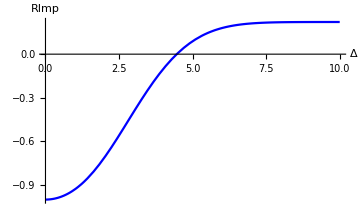

```mathematica
Plot[PsηRelativeImprovement[√0.75,√0.25,2,0,Δ,Δ,(*ϵ*)1/2,0.2,1],{Δ,0,10},AxesLabel->{Δ,RImp},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

```mathematica
ηmax[√0.75,√0.25,2,0,(*ϵ*)1/2,1]
```

{η→1.33333}

$Aborted

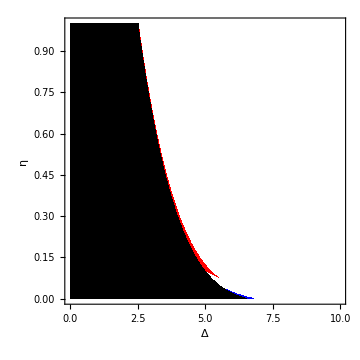

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that heterodyning is better to simulate certain efficiencies. Observation: α needs to be sufficienctly small. But be wary that too small α means we need bigger Δ. *)
plotRO = DensityPlot[HeavisideTheta[ηRelativeOverlap[√0.75,√0.25,3,0,Δ,Δ,(*ϵ*)1/2,η,1]],{Δ,0,10},{η,0,1},PlotPoints->60,ColorFunction->(Blend[{RGBColor[0,0,1,1],RGBColor[1,0,0,1]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
plotRI=DensityPlot[HeavisideTheta[PsηRelativeImprovement[√0.75,√0.25,3,0,Δ,Δ,(*ϵ*)1/2,η,1]],{Δ,0,10},{η,0,1},PlotPoints->60,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0.3]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{Δ,η},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium];
Show[{plotRO,plotRI}]
```

```mathematica
(* Numerically fnding the point where Threshold and Heterodyne detections are equivalent, i.e. where RO(η,Δ)==0 AND RI(η,Δ)==0 *)
```

```mathematica
EquivalencePoint[√0.75,√(1-0.75),1.2,0,1/2]
```

{η→2.45542×10^-9,Δ→12.1118}

```mathematica
EquivalencePoint[t_,r_,α_,θ_,ϵ_]:=FindRoot[{ηRelativeOverlap[t,r,α,θ,Δ,Δ,ϵ,η,1]==0,PsηRelativeImprovement[t,r,α,θ,Δ,Δ,ϵ,η,1]==0},{{η,1},{Δ,1}}];
```

```mathematica
ClearAll[list,arg];
list[ϵ_,t_,θ_,αmin_,αmax_,dα_]:=({η,#,Δ}/.EquivalencePoint[t,√(1-t^2),#,θ,ϵ])&/@Range[αmin,αmax,dα];
Quiet[arg=list[(*ϵ*)1/2,#,0,0,1,0.1]&/@Range[√0.5,1,0.01];]
```

```mathematica
plotlist=ListPointPlot3D[arg[[#]],PlotRange->{{0,1},Automatic,Automatic},AxesLabel->{η,α,Δ},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->RGBColor[0,0,#/(Dimensions[arg][[1]]),0.8#/(Dimensions[arg][[1]])]]&/@Range[Dimensions[arg][[1]]];
```

```mathematica
Show[plotlist]
```

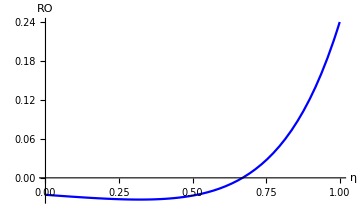

```mathematica
(* Limiting function assuming lim Δ->0^+ gives ηmax. Not true as there could be some minimum Δ beyond which there is a solution. For example see the case of α = 1.2. It doesn't start at Δ=0.s *)
Plot[LimitingFunction[√0.75,√0.25,2,0,η,1],{η,0,1},AxesLabel->{η,RO},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {η} = {-14.8744}. Try perturbing the initial point(s).

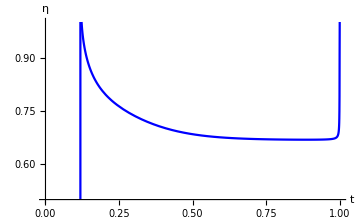

```mathematica
(* Behavior with beamsplitter trasmittivity starts at √0.5 *)
Plot[η/.ηmax[√T,√(1-T),2,0,1],{T,0,1},PlotRange->{0.5,1},AxesLabel->{t,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

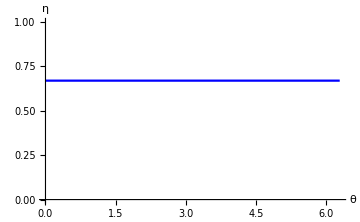

```mathematica
(* Behavior with θ *)
Plot[η/.ηmax[√0.75,√0.25,2,θ,1],{θ,0,2π},PlotRange->{0,1},AxesLabel->{θ,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {η} = {1.}. Try perturbing the initial point(s).

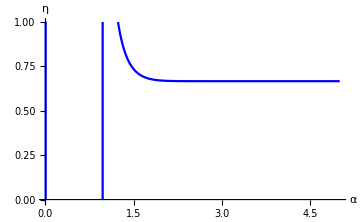

```mathematica
(* Behavior with α *)
Plot[η/.ηmax[√0.75,√0.25,α,0,1],{α,0,5},PlotRange->{0,1},AxesLabel->{α,η},PlotStyle->Blue,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium]
```

```mathematica
(* There are several unphysical parameter spaces one needs to be wary about *)
```

Fixing Δ finding η

```mathematica
WnHetero[√0.75,√0.25,2,0,0,0,2,2,1]
```

0.125279

Heterodyne success probability:

0.00253249

{η→0.68401}

Threshold success probability:

0.255842

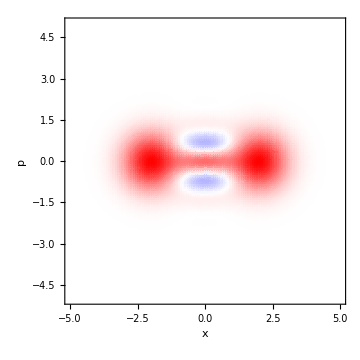
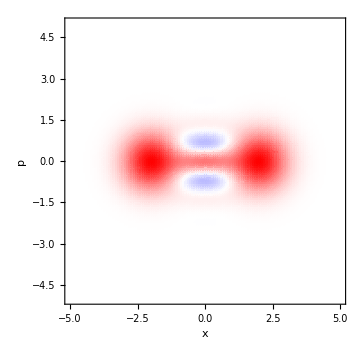
(a) Threshold | (b) Heterodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δ,Δp,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ=0;
s=1; (* s-cat *)
Δ=Δp=0.3;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
r=√(1-t^2);

(* Psuccess *)
"Heterodyne success probability: "
Re[PsHetero[t,r,α,θ,Δ,Δp,s]]


matWnHetero=Table[Re[Chop[WnHetero[t,r,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ,Δp,s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnHetero =matWnHetero/(Abs[ Total[matWnHetero,2]](limits/range)^2);

(*model=WnThreshold[t,α,θ,x,p,η,s];
range =(Dimensions[matWnHetero ][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWnHetero [[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]*)
fit =ηmax[t,r,α,θ,s]

matWnThreshold=Table[Re[Chop[WnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit,s]]],{p,1,2 range +1},{x,1,2 range +1}];
matWnThreshold=matWnThreshold/(Abs[Total[matWnThreshold,2]](limits/range)^2);
"Threshold success probability: "
PsThreshold[t,α,η/.fit,s]

plotThreshold=ListDensityPlot[matWnThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnThreshold]],Abs[Min[matWnThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHeterodyne=ListDensityPlot[matWnHetero,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWnHetero]],Abs[Min[matWnHetero]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Heterodyne"},{plotThreshold,plotHeterodyne}}]
```

Comparing P_S for odd cat states w.r.t. θ

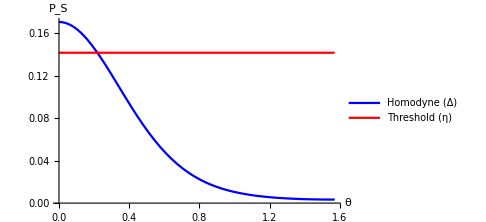

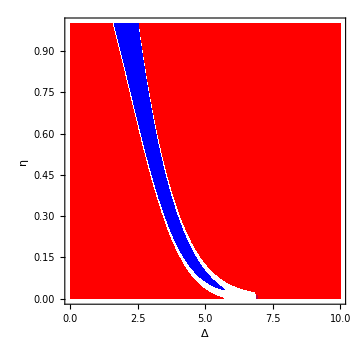

```mathematica
Plot[{Ps[t,√(1-t^2),α,θ,Δ], PsThreshold[t,α,η/.fit]},{θ,0,π/2},AxesLabel->{θ,Subscript[P, S]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->{"Homodyne (Δ)","Threshold (η)"}]
```